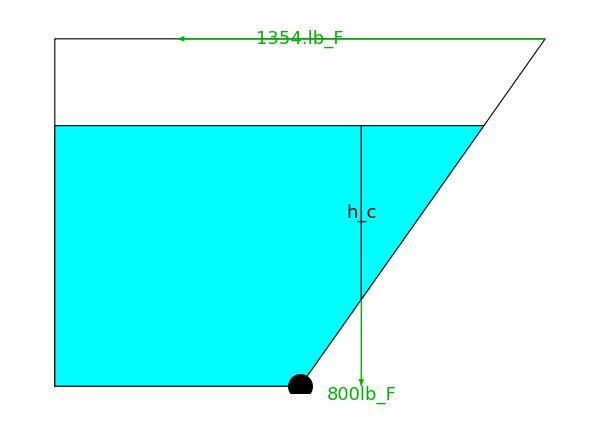

```mathematica
Module[{a1,a2,b,h1,h2,A,θ,yc,hc,γ,FR,W,Ixc,yR,FT},
a1=6;a2=8;b=4;A=a1*b;
h1=a1*Sin[θ];h2=a2*Sin[θ];
θ=60°;yc=a1/2;hc=yc*Sin[θ];
γ=62.4;(*lbF/ft3*)

FR=γ*hc*A;W=800;(*lb*)
Ixc=1/12*b*a1^3;yR=yc+Ixc/(yc*A);
FT=f/.Quiet@Solve[FR*(a1-yR)+W*b*Cos[θ]==f*a2*Sin[θ],f][[1]];


Graphics[{EdgeForm@Thick,Thick,Arrowheads@0.05,
{FaceForm@None,Polygon[{{0,h2},{0,0},{b,0},{b+a2*Cos[θ],h2}}]},
{FaceForm@Cyan,Polygon[{{0,h1},{0,0},{b,0},{b+a1*Cos[θ],h1}}]},
{PointSize@0.03,Point@{b,0}},

Line[{{b+a1*Cos[θ]-2,h1},{b+a1*Cos[θ]-2,1.72}}],
Text[Style[Subscript[Style["h",Italic],"c"],18,Background->Cyan],{b+a1*Cos[θ]-2,(h1+1.72)/2}],

{RGBColor[0,0.7,0],Arrow[{{b+a2*Cos[θ],h2},{2,h2}}],
Text[Style[Row@{NumberForm[FT,{4,0}],Subscript[" lb","F"]},18,Background->White],{b,h2}],

Arrow[{{b+a1*Cos[θ]-2,1.72},{b+a1*Cos[θ]-2,0}}],
Text[Style[Row@{W,Subscript[" lb","F"]},18],{b+a1*Cos[θ]-2,0},{0,1}],

}
},ImageSize->{600,425}]
]
```

```mathematica
Solve[Sin[θ]==(h1-y)/((h1-y)^2+2^2),y]
```

{{y→1/2 Csc[θ] (-1-√(-7+8 Cos[2 θ])+2 h1 Sin[θ])},{y→1/2 Csc[θ] (-1+√(-7+8 Cos[2 θ])+2 h1 Sin[θ])}}

```mathematica
Solve[Sin[θ]==y/((y)^2+2^2),y]
```

{{y→1/2 (1+√(-7+8 Cos[2 θ])) Csc[θ]},{y→1/2 (Csc[θ]-√(-7+8 Cos[2 θ]) Csc[θ])}}